```mathematica
SetDirectory["~/sync/data/multissdb/Top8000-best_hom50_pdb_chain"];
```

```mathematica
data = Map[Association[Import[#,"JSON"]]&,FileNames[]];
```

```mathematica
all3= Merge[Map[Counts[#["All3"]]&,data],Total];
dssp3 = Merge[Map[Counts[#["Dssp3"]]&,data],Total];
stride3 = Merge[Map[Counts[#["Stride3"]]&,data],Total];
kaksi3 = Merge[Map[Counts[#["Kaksi3"]]&,data],Total];
pross3 = Merge[Map[Counts[#["Pross3"]]&,data],Total];
```

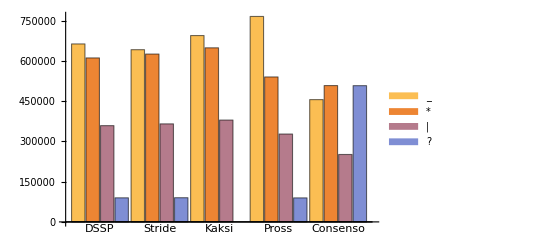

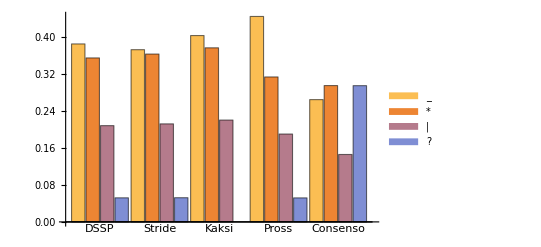

```mathematica
BarChart[{dssp3, stride3, kaksi3, pross3,all3}, ChartLabels->{{"DSSP","Stride","Kaksi","Pross","Consenso"}, None}, ChartLegends->Automatic]
BarChart[{dssp3, stride3, kaksi3, pross3,all3}/Total[Values[all3]], ChartLabels->{{"DSSP","Stride","Kaksi","Pross","Consenso"}, None}, ChartLegends->Automatic]
```

```mathematica
Clear[data];
ClearSystemCache[];
MemoryInUse[]
```

6929997664

```mathematica
SetDirectory["~/sync/data/multissdb/Top8000-best_hom70_pdb_chain"];
```

```mathematica
data = Map[Association[Import[#,"JSON"]]&,FileNames[]];
```

Import::fmterr: Cannot import data as JSON format.

General::stop: Further output of Import::fmterr will be suppressed during this calculation.

$Aborted

```mathematica
all3= Merge[Map[Counts[#["All3"]]&,data],Total];
dssp3 = Merge[Map[Counts[#["Dssp3"]]&,data],Total];
stride3 = Merge[Map[Counts[#["Stride3"]]&,data],Total];
kaksi3 = Merge[Map[Counts[#["Kaksi3"]]&,data],Total];
pross3 = Merge[Map[Counts[#["Pross3"]]&,data],Total];
```

```mathematica
BarChart[{dssp3, stride3, kaksi3, pross3,all3}, ChartLabels->{{"DSSP","Stride","Kaksi","Pross","Consenso"}, None}, ChartLegends->Automatic]
BarChart[{dssp3, stride3, kaksi3, pross3,all3}/Total[Values[all3]], ChartLabels->{{"DSSP","Stride","Kaksi","Pross","Consenso"}, None}, ChartLegends->Automatic]
```

```mathematica
SetDirectory["~/sync/data/multissdb/Top8000-best_hom95_pdb_chain"];
```

```mathematica
data = Map[Association[Import[#,"JSON"]]&,FileNames[]];
```

```mathematica
all3= Merge[Map[Counts[#["All3"]]&,data],Total];
dssp3 = Merge[Map[Counts[#["Dssp3"]]&,data],Total];
stride3 = Merge[Map[Counts[#["Stride3"]]&,data],Total];
kaksi3 = Merge[Map[Counts[#["Kaksi3"]]&,data],Total];
pross3 = Merge[Map[Counts[#["Pross3"]]&,data],Total];
```

```mathematica
BarChart[{dssp3, stride3, kaksi3, pross3,all3}, ChartLabels->{{"DSSP","Stride","Kaksi","Pross","Consenso"}, None}, ChartLegends->Automatic]
BarChart[{dssp3, stride3, kaksi3, pross3,all3}/Total[Values[all3]], ChartLabels->{{"DSSP","Stride","Kaksi","Pross","Consenso"}, None}, ChartLegends->Automatic]
```

```mathematica
SetDirectory["~/sync/data/multissdb/chameleonic-10"];
```

```mathematica
data = Map[Association[Import[#,"JSON"]]&,FileNames[]];
```

```mathematica
all3= Merge[Map[Counts[#["All3"]]&,data],Total];
dssp3 = Merge[Map[Counts[#["Dssp3"]]&,data],Total];
stride3 = Merge[Map[Counts[#["Stride3"]]&,data],Total];
kaksi3 = Merge[Map[Counts[#["Kaksi3"]]&,data],Total];
pross3 = Merge[Map[Counts[#["Pross3"]]&,data],Total];
```

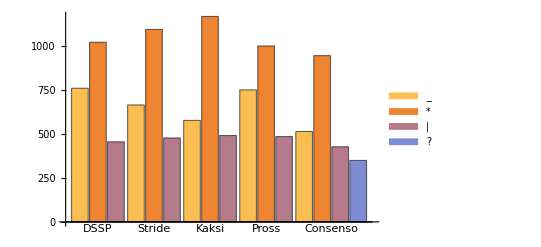

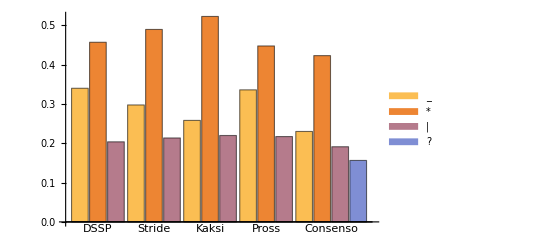

```mathematica
BarChart[{dssp3, stride3, kaksi3, pross3,all3}, ChartLabels->{{"DSSP","Stride","Kaksi","Pross","Consenso"}, None}, ChartLegends->Automatic]
BarChart[{dssp3, stride3, kaksi3, pross3,all3}/Total[Values[all3]], ChartLabels->{{"DSSP","Stride","Kaksi","Pross","Consenso"}, None}, ChartLegends->Automatic]
```

```mathematica
data
```

data